# Perturbation methods

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
Simplify[DSolve[{y''[t]+y'[t]==(y[t])^2,y[0]==0,y'[0]==v0},y[t],t]]
```

DSolve[{y[t]^2==y'[t]+y''[t],y[0]==0,v0==y'[0]},y[t],t]

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
Simplify[DSolve[{y1''[t]==y1[t],y1[0]==0,y1'[0]==v0},y1[t],t]]
```

{{y1[t]→1/2 ⅇ^-t (-1+ⅇ^(2 t)) v0}}

```mathematica
Remove["Global`*"];SetDirectory[NotebookDirectory[]];<<ToMatlab.m
y1=1/2 ⅇ^-t (-1+ⅇ^(2 t)) v0;
dy1=D[y1,t];
ddy1=D[dy1,t];
Simplify[DSolve[{y2''[t]+ddy1+dy1+y2'[t]==y1+y2[t],y2[0]==0,y2'[0]==0},y2[t],t]]
y2=-1/10 (-5 ⅇ^-t+5 ⅇ^t-2 √5 ⅇ^(1/2 (-1+√5) t)+2 √5 ⅇ^(-1/2 (1+√5) t)) v0;
Simplify[y1+y2]
```

{{y2[t]→-1/10 (-5 ⅇ^-t+5 ⅇ^t-2 √5 ⅇ^(1/2 (-1+√5) t)+2 √5 ⅇ^(-1/2 (1+√5) t)) v0}}

(ⅇ^(-1/2 (1+√5) t) (-1+ⅇ^(√5 t)) v0)/(√5)

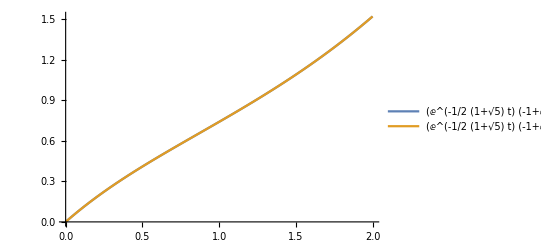

```mathematica
v0=1;
Plot[{(ⅇ^(-1/2 (1+√5) t) (-1+ⅇ^(√5 t)) v0)/(√5),(ⅇ^(-1/2 (1+√5) t) (-1+ⅇ^(√5 t)) v0)/(√5)},{t,0,2},PlotLegends->"Expressions"]
```

```mathematica
y1=1/2 ⅇ^-t (-1+ⅇ^(2 t)) v0;
y2=1/10 ⅇ^(-1/2 (3+√5) t) (-((5+√5) ⅇ^t)+10 ⅇ^(1/2 (1+√5) t)+(-5+√5) ⅇ^(t+√5 t)) v0;
dy1=D[y1,t];
ddy1=D[dy1,t];
FullSimplify[DSolve[{y2''[t]+ddy1+dy1+y2'[t]==y1+y2[t],y2[0]==0,y2'[0]==0},y2[t],t]]
y2=1/10 ⅇ^(-1/2 (3+√5) t) (-((5+√5) ⅇ^t)+10 ⅇ^(1/2 (1+√5) t)+(-5+√5) ⅇ^(t+√5 t)) v0;
Simplify[y1+y2]
```